## Mathematica Computation of Magnetization Vector

## Computation (Cross Product -> NDSolver)

```mathematica
Inputs;
```

```mathematica
f=1;
```

```mathematica
Hz=0.1;
```

```mathematica
mm=21/(4 π);
```

```mathematica
x0=0;
```

```mathematica
y0=21/(4 π √2);
```

```mathematica
z0=21/(4 π √2);
```

```mathematica
γ=2.9 2 π;
```

```mathematica
α=0.01;
```

```mathematica
M[x_,y_,z_]:={x,y,z};
```

```mathematica
H[hx_,t_,x_,y_,z_]:={hx*Cos[2 π f t]-4 π x,-4 π y,Hz-4 π z};
```

```mathematica
mxh[hx_,t_,x_,y_,z_]:=Cross[M[x,y,z],H[hx,t,x,y,z]];
```

```mathematica
eqs[hx_,t_,x_,y_,z_]:=(γ*(mxh[hx,t,x,y,z]-(α*Cross[M[x,y,z],mxh[hx,t,x,y,z]])/Sqrt[M[x,y,z].M[x,y,z]]))/(1+α^2);
```

```mathematica
fx[hx_,t_,x_,y_,z_]:=Part[eqs[hx,t,x,y,z],1];
```

```mathematica
fy[hx_,t_,x_,y_,z_]:=Part[eqs[hx,t,x,y,z],2];
```

```mathematica
fz[hx_,t_,x_,y_,z_]:=Part[eqs[hx,t,x,y,z],3];
```

```mathematica
rk2[hx_,t0_,tf_,h_]:=Module[{n,t,x,y,z,i,j,k1x,k2x,k3x,k4x,k1y,k2y,k3y,k4y,k1z,k2z,k3z,k4z},n=(tf-t0)/h;
t=Table[j,{j,1,n+1}];
x=Table[j,{j,1,n+1}];
y=Table[j,{j,1,n+1}];
z=Table[j,{j,1,n+1}];
t[[1]]=t0;x[[1]]=x0;y[[1]]=y0;z[[1]]=z0;
Do[k1x=fx[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k1y=fy[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k1z=fz[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k2x=fx[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k2y=fy[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k2z=fz[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
t[[i+1]]=t[[i]]+h;
x[[i+1]]=x[[i]]+h*k2x;
y[[i+1]]=y[[i]]+h*k2y;
z[[i+1]]=z[[i]]+h*k2z;,
{i,1,n}];{x,y,z}];
```

```mathematica
rk2yEx[hx_,t0_,tf_,h_,res_,name_]:=
Module[{n,t,x,y,z,ttemp,xtemp,ytemp,ztemp,i,j,k,k1x,k2x,k3x,k4x,k1y,k2y,k3y,k4y,k1z,k2z,k3z,k4z,str,cut},
str = OpenAppend[ToString[name]];
n=IntegerPart[(tf-t0)/h];
cut = IntegerPart[res/h];
ttemp=t0;xtemp=x0;ytemp=y0;ztemp=z0;
WriteString[str,ToString[N[y0,11]],"\n"];
Do[
t = Table[k,{k,1,cut+1}];
x = Table[k,{k,1,cut+1}];
y = Table[k,{k,1,cut+1}];
z = Table[k,{k,1,cut+1}];
t[[1]]=ttemp;
x[[1]] = xtemp;
y[[1]] = ytemp;
z[[1]] = ztemp;
Do[
k1x=fx[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k1y=fy[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k1z=fz[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k2x=fx[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k2y=fy[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k2z=fz[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
t[[i+1]]=t[[i]]+h;
x[[i+1]]=x[[i]]+h*k2x;
y[[i+1]]=y[[i]]+h*k2y;
z[[i+1]]=z[[i]]+h*k2z;,
{i,1,cut}];
WriteString[str,ToString[NumberForm[Part[y,cut+1],{11,10},ExponentFunction->(Null&)]],"\n"];
ttemp=t[[cut+1]];
xtemp=x[[cut+1]];
ytemp=y[[cut+1]];
ztemp=z[[cut+1]];
ClearAll[x,y,z,t];,{j,1,IntegerPart[n/cut]}];
Close[str];];
```

```mathematica
rk4[hx_,t0_,tf_,h_]:=Module[{n,t,x,y,z,i,j,k1x,k2x,k3x,k4x,k1y,k2y,k3y,k4y,k1z,k2z,k3z,k4z},n=(tf-t0)/h;
t=Table[j,{j,1,n+1}];
x=Table[j,{j,1,n+1}];
y=Table[j,{j,1,n+1}];
z=Table[j,{j,1,n+1}];
t[[1]]=t0;x[[1]]=x0;y[[1]]=y0;z[[1]]=z0;
Do[k1x=fx[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k1y=fy[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k1z=fz[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k2x=fx[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k2y=fy[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k2z=fz[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k3x=fx[hx,t[[i]]+h/2,x[[i]]+h/2*k2x,y[[i]]+h/2*k2y,z[[i]]+h/2*k2z];
k3y=fy[hx,t[[i]]+h/2,x[[i]]+h/2*k2x,y[[i]]+h/2*k2y,z[[i]]+h/2*k2z];
k3z=fz[hx,t[[i]]+h/2,x[[i]]+h/2*k2x,y[[i]]+h/2*k2y,z[[i]]+h/2*k2z];
k4x=fx[hx,t[[i]]+h,x[[i]]+h*k3x,y[[i]]+h*k3y,z[[i]]+h*k3z];
k4y=fy[hx,t[[i]]+h,x[[i]]+h*k3x,y[[i]]+h*k3y,z[[i]]+h*k3z];
k4z=fz[hx,t[[i]]+h,x[[i]]+h*k3x,y[[i]]+h*k3y,z[[i]]+h*k3z];
t[[i+1]]=t[[i]]+h;
x[[i+1]]=x[[i]]+h/6*(k1x+2*k2x+2*k3x+k4x);
y[[i+1]]=y[[i]]+h/6*(k1y+2*k2y+2*k3y+k4y);
z[[i+1]]=z[[i]]+h/6*(k1z+2*k2z+2*k3z+k4z);,{i,1,n}];{x,y,z}];
```

```mathematica
rk4yEx[hx_,t0_,tf_,h_,res_,name_]:=Module[{n,t,x,y,z,ttemp,xtemp,ytemp,ztemp,i,j,k,k1x,k2x,k3x,k4x,k1y,k2y,k3y,k4y,k1z,k2z,k3z,k4z,str,cut},str=OpenAppend[ToString[name]];
n=IntegerPart[(tf-t0)/h];
cut=IntegerPart[res/h];
ttemp=t0;xtemp=x0;ytemp=y0;ztemp=z0;
WriteString[str,ToString[N[y0,11]],"\n"];
Do[t=Table[k,{k,1,cut+1}];
x=Table[k,{k,1,cut+1}];
y=Table[k,{k,1,cut+1}];
z=Table[k,{k,1,cut+1}];
t[[1]]=ttemp;
x[[1]]=xtemp;
y[[1]]=ytemp;
z[[1]]=ztemp;
Do[k1x=fx[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k1y=fy[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k1z=fz[hx,t[[i]],x[[i]],y[[i]],z[[i]]];
k2x=fx[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k2y=fy[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k2z=fz[hx,t[[i]]+h/2,x[[i]]+h/2*k1x,y[[i]]+h/2*k1y,z[[i]]+h/2*k1z];
k3x=fx[hx,t[[i]]+h/2,x[[i]]+h/2*k2x,y[[i]]+h/2*k2y,z[[i]]+h/2*k2z];
k3y=fy[hx,t[[i]]+h/2,x[[i]]+h/2*k2x,y[[i]]+h/2*k2y,z[[i]]+h/2*k2z];
k3z=fz[hx,t[[i]]+h/2,x[[i]]+h/2*k2x,y[[i]]+h/2*k2y,z[[i]]+h/2*k2z];
k4x=fx[hx,t[[i]]+h,x[[i]]+h*k3x,y[[i]]+h*k3y,z[[i]]+h*k3z];
k4y=fy[hx,t[[i]]+h,x[[i]]+h*k3x,y[[i]]+h*k3y,z[[i]]+h*k3z];
k4z=fz[hx,t[[i]]+h,x[[i]]+h*k3x,y[[i]]+h*k3y,z[[i]]+h*k3z];
t[[i+1]]=t[[i]]+h;
x[[i+1]]=x[[i]]+h/6*(k1x+2*k2x+2*k3x+k4x);
y[[i+1]]=y[[i]]+h/6*(k1y+2*k2y+2*k3y+k4y);
z[[i+1]]=z[[i]]+h/6*(k1z+2*k2z+2*k3z+k4z);,{i,1,cut}];
WriteString[str,ToString[NumberForm[Part[y,cut+1],{11,10},ExponentFunction->(Null&)]],"\n"];
ttemp=t[[cut+1]];
xtemp=x[[cut+1]];
ytemp=y[[cut+1]];
ztemp=z[[cut+1]];
ClearAll[x,y,z,t];,{j,1,IntegerPart[n/cut]}];
Close[str];];
```

```mathematica
x1[hx_,t0_,tf_,step_]:=Part[rk4[hx,t0,tf,step],1];
```

```mathematica
y1[hx_,t0_,tf_,step_]:=Part[rk4[hx,t0,tf,step],2];
```

```mathematica
z1[hx_,t0_,tf_,step_]:=Part[rk4[hx,t0,tf,step],3];
```

#### LSODA / RK4 Implicit

```mathematica
MImp={x[t],y[t],z[t]};
```

```mathematica
HImp[hx_]={hx*Cos[2 π f t]-4 π x[t],-4 π y[t],Hz-4 π z[t]};
```

```mathematica
mxhImp[hx_]:=MImp×HImp[hx];
```

```mathematica
eqsImp[hx_]:=(γ*(mxhImp[hx]-(α*Cross[MImp,mxhImp[hx]])/Sqrt[MImp.MImp]))/(α^2+1);
```

```mathematica
LSODA[hx_,t0_,tf_,step_]:=NDSolve[{Derivative[1][x][t]==Part[eqsImp[hx],1],Derivative[1][y][t]==Part[eqsImp[hx],2],Derivative[1][z][t]==Part[eqsImp[hx],3],x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,t0,tf},MaxSteps->Infinity,MaxStepSize->step];
```

```mathematica
x1LSODA[hx_,t0_,tf_,step_]:=(x[t]/.LSODA[hx,t0,tf,step])[[1]];
```

```mathematica
y1LSODA[hx_,t0_,tf_,step_]:=(y[t]/.LSODA[hx,t0,tf,step])[[1]];
```

```mathematica
z1LSODA[hx_,t0_,tf_,step_]:=(z[t]/.LSODA[hx,t0,tf,step])[[1]];
```

```mathematica
ClassicalRungeKutta[___]["Step"[f_,t_,h_,y_,yp_]]:=Block[{deltay,k1,k2,k3,k4},k1=yp;
k2=f[t+1/2 h,y+1/2 h k1];
k3=f[t+1/2 h,y+1/2 h k2];
k4=f[t+h,y+h k3];
deltay=h (1/6 k1+1/3 k2+1/3 k3+1/6 k4);
{h,deltay}];
```

```mathematica
rk4Imp[hx_,t0_,tf_,step_]:=NDSolve[{Derivative[1][x][t]==Part[eqsImp[hx],1],Derivative[1][y][t]==Part[eqsImp[hx],2],Derivative[1][z][t]==Part[eqsImp[hx],3],x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,t0,tf},MaxSteps->Infinity,StartingStepSize->step,Method->ClassicalRungeKutta];
```

```mathematica
x1rk4Imp[hx_,t0_,tf_,step_]:=(x[t]/.rk4Imp[hx,t0,tf,step])[[1]];
```

```mathematica
y1rk4Imp[hx_,t0_,tf_,step_]:=(y[t]/.rk4Imp[hx,t0,tf,step])[[1]];
```

```mathematica
z1rk4Imp[hx_,t0_,tf_,step_]:=(z[t]/.rk4Imp[hx,t0,tf,step])[[1]];
```

## Data Generation

```mathematica
xdata[hx_,BeginInterval_,EndInterval_,step_,res_] := ($a=x1rk4Imp[hx,BeginInterval,EndInterval,step];Table[$a,{t,BeginInterval,EndInterval,res}]);
```

```mathematica
ydata[hx_,BeginInterval_,EndInterval_,step_,res_] := ($a=y1rk4Imp[hx,BeginInterval,EndInterval,step];Table[$a,{t,BeginInterval,EndInterval,res}]);
```

```mathematica
zdata[hx_,BeginInterval_,EndInterval_,step_,res_] := ($a=z1rk4Imp[hx,BeginInterval,EndInterval,step];Table[$a,{t,BeginInterval,EndInterval,res}]);
```

```mathematica
tt[BeginInterval_,EndInterval_,res_] := Table[t,{t,BeginInterval,EndInterval,res}];
```

```mathematica
xff[hx_,BeginInterval_,EndInterval_,step_,res_]:=Abs[Fourier[xdata[hx,BeginInterval,EndInterval,step,res]]];
```

```mathematica
yff[hx_,BeginInterval_,EndInterval_,step_,res_]:=Abs[Fourier[ydata[hx,BeginInterval,EndInterval,step,res]]];
```

```mathematica
zff[hx_,BeginInterval_,EndInterval_,step_,res_]:=Abs[Fourier[zdata[hx,BeginInterval,EndInterval,step,res]]];
```

```mathematica
ff[hx_,BeginInterval_,EndInterval_,step_,res_]:=Table[i,{i,0,Length[yff[hx,BeginInterval,EndInterval,step,res]]-1}]*1/res/Length[yff[hx,BeginInterval,EndInterval,step,res]];
```

```mathematica
xffd[hx_,BeginInterval_,EndInterval_,step_,res_]:=Part[xff[hx,BeginInterval,EndInterval,step,res],1;;Round[Length[xff[hx,BeginInterval,EndInterval,step,res]]/2]];(*FFT Data to analyze*)
```

```mathematica
yffd[hx_,BeginInterval_,EndInterval_,step_,res_]:=Part[yff[hx,BeginInterval,EndInterval,step,res],1;;Round[Length[yff[hx,BeginInterval,EndInterval,step,res]]/2]];(*FFT Data to analyze*)
```

```mathematica
zffd[hx_,BeginInterval_,EndInterval_,step_,res_]:=Part[zff[hx,BeginInterval,EndInterval,step,res],1;;Round[Length[zff[hx,BeginInterval,EndInterval,step,res]]/2]];(*FFT Data to analyze*)
```

```mathematica
ffd[hx_,BeginInterval_,EndInterval_,step_,res_]:=Part[ff[hx,BeginInterval,EndInterval,step,res],1;;Round[Length[ff[hx,BeginInterval,EndInterval,step,res]]/2]];       (*Modified Freq. List*)
```

## Data Export

```mathematica
xtEx[hx_,BeginInterval_,EndInterval_,step_,res_]:=($a=xdata[hx,BeginInterval,EndInterval,step,res];Export[StringJoin[ToString[hx*100],"dat"],$a];)
```

```mathematica
ytEx[hx_,BeginInterval_,EndInterval_,step_,res_]:=($a=ydata[hx,BeginInterval,EndInterval,step,res];
Export[StringJoin[ToString[hx],".dat"],$a];)
```

```mathematica
yrk2Ex[hx_,t0_,tf_,step_,res_,name_]:= rk2yEx[hx,t0,tf,step,res,name];
```

```mathematica
yrk4Ex[hx_,t0_,tf_,step_,res_,name_]:= rk4yEx[hx,t0,tf,step,res,name];
```

```mathematica
yLSODAEx[hx_,t0_,tf_,step_,res_,name_]:= (str=OpenAppend[ToString[name]];$a=y1rk4Imp[hx,t0,tf,step];
Do[WriteString[str,ToString[NumberForm[$a,{11,10},ExponentFunction->(Null&)]],"\n"],{t,t0,tf,res}]
Close[str];)
```

```mathematica
yrk4ImpEx[hx_,t0_,tf_,step_,res_,name_]:= (str=OpenAppend[ToString[name]];$a=y1rk4Imp[hx,t0,tf,step];
Do[WriteString[str,ToString[NumberForm[$a,{11,10},ExponentFunction->(Null&)]],"\n"],{t,t0,tf,res}]
Close[str];)
```

```mathematica
ytExStream[hx_,BeginInterval_,EndInterval_,step_,res_,name_]:=($a=y1rk4Imp[hx,BeginInterval,EndInterval,step];$out = OpenWrite[ToString[name]];Do[Write[$out,$a],{t,BeginInterval,EndInterval,res}];Close[$out];)
```

```mathematica
ytExStream1[hx_,BeginInterval_,EndInterval_,step_,res_,name_]:=($a=y1rk4Imp[hx,BeginInterval,EndInterval,step];Do[$a>>> {ToString[name]},{t,BeginInterval,EndInterval,res}];)
```

```mathematica
ytExStream2[hx_,BeginInterval_,EndInterval_,step_,res_,name_]:=(str=OpenAppend[ToString[name]];$a=y1rk4Imp[hx,BeginInterval,EndInterval,step];
Do[WriteString[str,ToString[$a,InputForm],"\n"],{t,BeginInterval,EndInterval,res}]
Close[str];)
```

```mathematica
ztEx[hx_,BeginInterval_,EndInterval_,step_,res_]:=($a=zdata[hx,BeginInterval,EndInterval,step,res];Export[StringJoin[ToString[IntegerPart[hx*100]],".dat"],$a];)
```

```mathematica
xfEx[hx_,BeginInterval_,EndInterval_,step_,res_]:=($a=xffd[hx,BeginInterval,EndInterval,step,res];Export[StringJoin[ToString[hx*100],"dat"],$a];)
```

```mathematica
yfEx[hx_,BeginInterval_,EndInterval_,step_,res_]:=($a=yffd[hx,BeginInterval,EndInterval,step,res];Export[StringJoin[ToString[hx*100],"dat"],$a];)
```

```mathematica
zfEx[hx_,BeginInterval_,EndInterval_,step_,res_]:=($a=zffd[hx,BeginInterval,EndInterval,step,res];Export[StringJoin[ToString[hx*100],"dat"],$a];)
```

## Plotting Functions (M(t) and 3D)

```mathematica
xtplot[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step,res],xdata[hx,BeginInterval,EndInterval,step,res]}],PlotRange->All,AxesLabel->{t,Mx}];
```

```mathematica
ytplot[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,res],ydata[hx,BeginInterval,EndInterval,step,res]}],PlotRange->All,AxesLabel->{t,My}];
```

```mathematica
ztplot[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,res],zdata[hx,BeginInterval,EndInterval,step,res]}],PlotRange->All,AxesLabel->{t,Mz}];
```

```mathematica
(* List Point Plot 3D *)
mtplot[hx_,BeginInterval_,EndInterval_,step_,res_]:=ListPointPlot3D[Transpose[{xdata[hx,BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res],zdata[hx,BeginInterval,EndInterval,step,res]}],AxesLabel->{"M_x","M_y","M_z"},PlotLabel->Style["3D Plot",FontSize->14,Bold]];
```

```mathematica
(* Sphere w/ vector Plot 3D *)
mtplot1[hx_,BeginInterval_,EndInterval_,step_,res_]:=Show[
Graphics3D[{Blue,AbsoluteThickness[1],Arrowheads[.05],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step,res]],Last[ydata[hx,BeginInterval,EndInterval,step,res]],Last[zdata[hx,BeginInterval,EndInterval,step,res]]}},0.02]]}],
Graphics3D[{Sphere[{0,0,0},0.5]}],
Boxed->False,ImageSize->800,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Vector Only 3D *)
mtplot2[hx_,BeginInterval_,EndInterval_,step_,res_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res],zdata[hx,BeginInterval,EndInterval,step,res]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Cambria(body)",30,Italic],{2.5,0,0}],
Text[Style["y",FontFamily->"Cambria(body)",30,Italic],{0,2.5,0}],
Text[Style["z",FontFamily->"Cambria(body)",30,Italic],{0,0,2.5}]}],
Graphics3D[{Blue,AbsoluteThickness[1],Arrowheads[.05],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step,res]],Last[ydata[hx,BeginInterval,EndInterval,step,res]],Last[zdata[hx,BeginInterval,EndInterval,step,res]]}},0.02]]}],
ImageSize->800,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* 3D Precession Path w/ Hz *)
mtplot3[hx_,BeginInterval_,EndInterval_,step_,res_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res],zdata[hx,BeginInterval,EndInterval,step,res]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,2.1},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Cambria(body)",30,Italic],{2.5,0,0}],
Text[Style["y",FontFamily->"Cambria(body)",30,Italic],{0,2.5,0}],
Text[Style["z",FontFamily->"Cambria(body)",30,Italic],{0,0,2.5}]}],
Graphics3D[{Blue,AbsoluteThickness[1],Arrowheads[.05],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step,res]],Last[ydata[hx,BeginInterval,EndInterval,step,res]],Last[zdata[hx,BeginInterval,EndInterval,step,res]]}},0.02]]}],
Graphics3D[{Green,AbsoluteThickness[1],Arrowheads[.045],Arrow[Tube[{{0,0,0},{0,0,2.1}},0.018]],
Text[Style["H_z",FontFamily->"Cambria(body)",38,Italic,Bold,Black],{0,0.41,1.99}],
Text[Style[StringJoin[ToString[IntegerPart[EndInterval]]," ns"],FontFamily->"Cambria(body)",45,Blue],{0,2,2.3}]}],
ImageSize->800,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* 3D Precession Path w/ Hz and hx *)
mtplot4[hx_,BeginInterval_,EndInterval_,step_,res_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res],zdata[hx,BeginInterval,EndInterval,step,res]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,2.1},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{1,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Cambria(body)",30,Italic],{2.5,0,0}],
Text[Style["y",FontFamily->"Cambria(body)",30,Italic],{0,2.5,0}],
Text[Style["z",FontFamily->"Cambria(body)",30,Italic],{0,0,2.5}]}],
Graphics3D[{Blue,AbsoluteThickness[1],Arrowheads[.05],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step,res]],Last[ydata[hx,BeginInterval,EndInterval,step,res]],Last[zdata[hx,BeginInterval,EndInterval,step,res]]}},0.02]]}],
Graphics3D[{Green,AbsoluteThickness[1],Arrowheads[.045],Arrow[Tube[{{0,0,0},{0,0,2.1}},0.018]],
Text[Style["H_z",FontFamily->"Cambria(body)",38,Italic,Bold,Black],{0,0.41,1.99}]}],
Graphics3D[{Red,AbsoluteThickness[1],Arrowheads[.045],Arrow[Tube[{{0,0,0},{1,0,0}},0.018]],Arrow[Tube[{{0,0,0},{-1,0,0}},0.018]],
Text[Style["h_x",FontFamily->"Cambria(body)",38,Italic,Bold,Black],{0.54,0,0.27}],Inset[Style[StringJoin[ToString[IntegerPart[EndInterval]]," ns"],FontFamily->"Cambria(body)",45,Blue],{0,2,2.3}]}],
ImageSize->800,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Inset for hx vs theta *)
mtplotTheta1[hx_,BeginInterval_,EndInterval_,step_,res_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res],zdata[hx,BeginInterval,EndInterval,step,res]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Arial",14,Bold],{2.5,0,0}],
Text[Style["y",FontFamily->"Arial",14,Bold],{0,2.5,0}],
Text[Style["z",FontFamily->"Arial",14,Bold],{0,0,2.5}]}],
Graphics3D[{Red,AbsoluteThickness[2],Arrowheads[.09],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step,res]],Last[ydata[hx,BeginInterval,EndInterval,step,res]],Last[zdata[hx,BeginInterval,EndInterval,step,res]]}},0.06]]}],
ImageSize->200,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Inset for hx vs theta *)
mtplotTheta2[hx_,BeginInterval_,EndInterval_,step_,res_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res],zdata[hx,BeginInterval,EndInterval,step,res]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,0,1.6}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Arial",14,Bold],{2.5,0,0}],
Text[Style["y",FontFamily->"Arial",14,Bold],{0,2.5,0}],
Text[Style["z",FontFamily->"Arial",14,Bold],{0,0,1.8}]}],
Graphics3D[{Red,AbsoluteThickness[2],Arrowheads[.09],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step,res]],Last[ydata[hx,BeginInterval,EndInterval,step,res]],Last[zdata[hx,BeginInterval,EndInterval,step,res]]}},0.06]]}],
ImageSize->200,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Inset for hx vs theta, now arrow *)
mtplotTheta1n[hx_,BeginInterval_,EndInterval_,step_,res_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res],zdata[hx,BeginInterval,EndInterval,step,res]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Arial",14,Bold],{2.5,0,0}],
Text[Style["y",FontFamily->"Arial",14,Bold],{0,2.5,0}],
Text[Style["z",FontFamily->"Arial",14,Bold],{0,0,2.5}]}],
ImageSize->200,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Inset for hx vs theta no arrow *)
mtplotTheta2n[hx_,BeginInterval_,EndInterval_,step_,res_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res],zdata[hx,BeginInterval,EndInterval,step,res]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,0,1.6}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Arial",14,Bold],{2.5,0,0}],
Text[Style["y",FontFamily->"Arial",14,Bold],{0,2.5,0}],
Text[Style["z",FontFamily->"Arial",14,Bold],{0,0,1.8}]}],
ImageSize->200,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
xfplot[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step,res],xff[hx,BeginInterval,EndInterval,step,res]}],PlotRange->{{0,2},{0,All}},AxesLabel->{"f(GHz)","|Mx|"}];
```

```mathematica
yfplot[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step,res],yff[hx,BeginInterval,EndInterval,step,res]}],PlotRange->{{0,1.5},{0,All}},AxesLabel->{"f(GHz)","|My|"},PlotLabel->Style[EndInterval "ns",FontSize->14,Blue]];
```

```mathematica
zfplot[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step,res],zff[hx,BeginInterval,EndInterval,step,res]}],PlotRange->{{0,2},{0,All}},AxesLabel->{"f(GHz)","|Mz|"}];
```

```mathematica
(* Large Image y(t), 0-400ns *)
ytplot1[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res]}],
PlotRange->{{0,400},{-1.5,1.5}},
Frame->True,
FrameStyle->Thickness[0.005],
(*PlotLabel->Style["M_y(t)",FontFamily->"Cambria(body)",50,Italic],*)
FrameLabel->{"Time (ns)","m_y",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->30},FrameTicks->{{{0,0,{0.02,0},{Thickness[0.005]}},{50,,{0.01,0},{Thickness[0.005]}},{100,100,{0.02,0},{Thickness[0.005]}},{150,,{0.01,0},{Thickness[0.005]}},{200,200,{0.02,0},{Thickness[0.005]}},{250,,{0.01,0},{Thickness[0.005]}},{300,300,{0.02,0},{Thickness[0.005]}},{350,,{0.01,0},{Thickness[0.005]}},{400,400,{0.02,0},{Thickness[0.005]}},{450,,{0.01,0},{Thickness[0.005]}},{500,500,{0.02,0},{Thickness[0.005]}}},
{{-1,-1,{0.02,0},{Thickness[0.005]}},{-0.5,,{0.01,0},{Thickness[0.005]}},{0,0,{0.02,0},{Thickness[0.005]}},{0.5,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}}},None,None},
Axes->False,
PlotStyle->Thickness[0.003],
ImageSize->800]
```

```mathematica
(* Small y(t) inset *)
ytplot2[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res]}],
PlotRange->{{100,120},{-0.3,0.3}},
Frame->True,
FrameStyle->Thickness[0.005],
FrameTicks->{{{105,,{0.015,0},{Thickness[0.005]}},{110,,{0.03,0},{Thickness[0.005]}},{115,,{0.015,0},{Thickness[0.005]}}},
{{-.15,,{0.015,0},{Thickness[0.005]}},{0,,{0.03,0},{Thickness[0.005]}},{0.15,,{0.015,0},{Thickness[0.005]}}},None,None},
Axes->False,
PlotStyle->Thickness[0.008],
ImageSize->300]
```

```mathematica
(* Large y(t) including inset *)
ytplot3[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step,res],ydata[hx,BeginInterval,EndInterval,step,res]}],
PlotRange->{{0,400},{-1.5,1.5}},
Frame->True,
FrameStyle->Thickness[0.005],
(*PlotLabel->Style["M_y(t)",FontFamily->"Cambria(body)",50,Italic],*)
FrameLabel->{"Time (ns)","m_y",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->30},FrameTicks->{{{0,0,{0.02,0},{Thickness[0.005]}},{50,,{0.01,0},{Thickness[0.005]}},{100,100,{0.02,0},{Thickness[0.005]}},{150,,{0.01,0},{Thickness[0.005]}},{200,200,{0.02,0},{Thickness[0.005]}},{250,,{0.01,0},{Thickness[0.005]}},{300,300,{0.02,0},{Thickness[0.005]}},{350,,{0.01,0},{Thickness[0.005]}},{400,400,{0.02,0},{Thickness[0.005]}},{450,,{0.01,0},{Thickness[0.005]}},{500,500,{0.02,0},{Thickness[0.005]}}},
{{-1,-1,{0.02,0},{Thickness[0.005]}},{-0.5,,{0.01,0},{Thickness[0.005]}},{0,0,{0.02,0},{Thickness[0.005]}},{0.5,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}}},None,None},
(*{{-1,-1,{0.02,0},{Thickness[0.005]}},,{-.75,,{0.01,0},{Thickness[0.005]}},{-.5,-0.5,{0.02,0},{Thickness[0.005]}},{-.25,,{0.01,0},{Thickness[0.005]}},{0,0,{0.02,0},{Thickness[0.005]}},{.25,,{0.01,0},{Thickness[0.005]}},{0.5,0.5,{0.02,0},{Thickness[0.005]}},{.75,,{0.01,0},{Thickness[0.005]}},{1,1.0,{0.02,0},{Thickness[0.005]}},{1.25,,{0.01,0},{Thickness[0.005]}}},None,None}*)
Axes->False,
PlotStyle->Thickness[0.003],
ImageSize->800,
Epilog->Inset[ytplot2[0,100,120,0.1],{300,0.7}]]
```

```mathematica
(* FT y(t) Hz=100 *)
yfplot0[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step,res],yff[hx,BeginInterval,EndInterval,step,res]}],PlotRange->{{0,1.5},{0,21}},
Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["H_z=100 Oe",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"f (GHz)","Fourier Transform",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},FrameTicks->{{{0.25,,{0.01,0},{Thickness[0.005]}},{0.5,0.5,{0.02,0},{Thickness[0.005]}},{0.75,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}},{1.25,,{0.01,0},{Thickness[0.005]}},{1.5,1.5,{0.02,0},{Thickness[0.005]}}},{{0,0,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{10,10,{0.02,0},{Thickness[0.005]}},{15,,{0.01,0},{Thickness[0.005]}},{20,20,{0.02,0},{Thickness[0.005]}},{60,60,{0.02,0},{Thickness[0.005]}},{80,80,{0.02,0},{Thickness[0.005]}}},None,None},
PlotStyle->Thickness[0.005],
ImageSize->800,
Epilog->Inset[Style[IntegerPart[EndInterval]"ns",FontFamily->"Cambria(body)",45,Blue],{1.25,18}]]
(* Use with intervals of 20ns,   0.01 step*)
```

```mathematica
(* FT y(t) Hz=100, hx=100 *)
yfplot100[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step,res],yff[hx,BeginInterval,EndInterval,step,res]}],PlotRange->{{0,1.5},{0,20}},
Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Row[{Style["H_z=100 Oe, ",FontFamily->"Cambria(body)",50,Italic],Style["h_x=100 Oe",FontFamily->"Cambria(body)",50,Italic,Red]}],
FrameLabel->{"f (GHz)","Fourier Transform",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},FrameTicks->{{{0.25,,{0.01,0},{Thickness[0.005]}},{0.5,0.5,{0.02,0},{Thickness[0.005]}},{0.75,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}},{1.25,,{0.01,0},{Thickness[0.005]}},{1.5,1.5,{0.02,0},{Thickness[0.005]}}},{{0,0,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{10,10,{0.02,0},{Thickness[0.005]}},{15,,{0.01,0},{Thickness[0.005]}},{20,20,{0.02,0},{Thickness[0.005]}},{25,,{0.01,0},{Thickness[0.005]}},{60,60,{0.02,0},{Thickness[0.005]}},{80,80,{0.02,0},{Thickness[0.005]}}},None,None},
PlotStyle->Thickness[0.005],
ImageSize->800,
Epilog->Inset[Style[IntegerPart[EndInterval]"ns",FontFamily->"Cambria(body)",45,Blue],{1.25,18}]]
(* Use with intervals of 20ns, 0.01 step*)
```

```mathematica
(* FT y(t) Hz=100, hx=430 *)
yfplot430[hx_,BeginInterval_,EndInterval_,step_,res_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step,res],yff[hx,BeginInterval,EndInterval,step,res]}],
PlotRange->{{0,1.5},{0,28}},
Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Row[{Style["H_z=100 Oe, ",FontFamily->"Cambria(body)",50,Italic],Style["h_x=430 Oe",FontFamily->"Cambria(body)",50,Italic,Red]}],
FrameLabel->{"f (GHz)","Fourier Transform",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},FrameTicks->{{{0.25,,{0.01,0},{Thickness[0.005]}},{0.5,0.5,{0.02,0},{Thickness[0.005]}},{0.75,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}},{1.25,,{0.01,0},{Thickness[0.005]}},{1.5,1.5,{0.02,0},{Thickness[0.005]}}},{{0,0,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{10,10,{0.02,0},{Thickness[0.005]}},{15,,{0.01,0},{Thickness[0.005]}},{20,20,{0.02,0},{Thickness[0.005]}},{25,,{0.01,0},{Thickness[0.005]}},{60,60,{0.02,0},{Thickness[0.005]}},{80,80,{0.02,0},{Thickness[0.005]}}},None,None},
PlotStyle->Thickness[0.005],
ImageSize->800,
Epilog->Inset[Style[IntegerPart[EndInterval]"ns",FontFamily->"Cambria(body)",45,Blue],{1.25,25}]]
(* Use with intervals of 20ns, 0.01 step*)
```

## Time Amplitude Generation

```mathematica
ffPeakIndex[hx_,BeginInterval_,EndInterval_,step_,res_]:=Catch[Do[If[Part[ffd[hx,BeginInterval,EndInterval,step,res],i]> .3,Throw[i-1]],{i,Length[ffd[hx,BeginInterval,EndInterval,step,res]]}]];
```

```mathematica
xfData[hx_,BeginInterval_,EndInterval_,step_,res_]:=Part[xffd[hx,BeginInterval,EndInterval,step,res],1;;ffPeakIndex[hx,BeginInterval,EndInterval,step,res]];
```

```mathematica
yfData[hx_,BeginInterval_,EndInterval_,step_,res_]:=Part[yffd[hx,BeginInterval,EndInterval,step,res],1;;ffPeakIndex[hx,BeginInterval,EndInterval,step,res]];
```

```mathematica
zfData[hx_,BeginInterval_,EndInterval_,step_,res_]:=Part[zffd[hx,BeginInterval,EndInterval,step,res],1;;ffPeakIndex[hx,BeginInterval,EndInterval,step,res]];
```

```mathematica
xfMax[hx_,BeginInterval_,EndInterval_,step_.res_]:=Max[xfData[hx,BeginInterval,EndInterval,step,res]];
```

```mathematica
yfMax[hx_,BeginInterval_,EndInterval_,step_,res_]:=Max[yfData[hx,BeginInterval,EndInterval,step,res]];
```

```mathematica
zfMax[hx_,BeginInterval_,EndInterval_,step_,res_]:=Max[zfData[hx,BeginInterval,EndInterval,step,res]];
```

```mathematica
xAmpData[hx_,stop_,delta_,res_]:=Table[{(m+1)*delta,xfMax[hx,m*delta,(m+1)delta,0.1,res]},{m,0,stop/delta-1}];
```

```mathematica
yAmpData[hx_,stop_,delta_,res_]:=Table[{(m+1)*delta,yfMax[hx,m*delta,(m+1)delta,0.1,res]},{m,0,stop/delta-1}];
```

```mathematica
zAmpData[hx_,stop_,delta_,res_]:=Table[{(m+1)*delta,zfMax[hx,m*delta,(m+1)delta,0.1,res]},{m,0,stop/delta-1}];
```

```mathematica
TimeAmpData [step_, delta_] :=(* default step=0.1,delta=500 *)
  (ParallelDo[
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100"];
        data = Import[StringJoin[ToString[IntegerPart[hx*100]], ".dat"]];
        amp = Table[0, {Length[data]*step/delta}];
        Do[ffdata = Part[Abs[Fourier[Part[data, IntegerPart[i*delta/step + 1] ;; IntegerPart[(i + 1) delta/step + 1]]]], 1 ;; ffPeakIndex[hx, 0, delta, step]]; amp[[i + 1]] = Max[ffdata];, {i, 0, Length[data]*step/delta - 1}];
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100"];
        Export[StringJoin[ToString[IntegerPart[hx*100]], ".dat"], amp];
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100"];
        , {hx, 0, 1, 0.01}];)
```

```mathematica
TimeAmpDataP[hxName_,step_,delta_,res_]:=(*default step=0.1,delta=50*)(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/precision"];
data=Import[StringJoin[ToString[hxName],".dat"]];
amp=Table[0,{Length[data]*res/delta}];
freqPeak = ffPeakIndex[ToExpression[hxName],0,delta,step,res];
Do[ffdata=Part[Abs[Fourier[Part[data,IntegerPart[i*delta/res+1];;IntegerPart[(i+1) delta/res+1]]]],1;;freqPeak];
amp[[i+1]]=Max[ffdata];,{i,0,Length[data]*res/delta-1}];
SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/precision"];
Export[StringJoin[ToString[hxName],".dat"],amp];
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/precision"];)
```

```mathematica
TimeAmpDataTest[hx_,step_,delta_,res_]:=(*default step=0.1,delta=50*)(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_test"];
data=Import[StringJoin[ToString[hx],".dat"]];
amp=Table[0,{Length[data]*step/delta}];
Do[ffdata=Log10[Part[Abs[Fourier[Part[data,IntegerPart[i*delta/step+1];;IntegerPart[(i+1) delta/step+1]],FourierParameters->{1,-1}]],1;;ffPeakIndexT[hx,0,delta,step,res]]];
amp[[i+1]]=Max[ffdata];,{i,0,Length[data]*step/delta-1}];
SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100_test"];
Export[StringJoin[ToString[hx],".dat"],amp];
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_test"];)
```

```mathematica
ffPeakIndexT[hx_,BeginInterval_,EndInterval_,step_,res_]:=Catch[Do[If[Part[ffd[hx,BeginInterval,EndInterval,step,res],i]> .35,Throw[i-1]],{i,Length[ffd[hx,BeginInterval,EndInterval,step,res]]}]];
```

```mathematica
TimeThetaData [step_, delta_] :=(* default step=0.1,delta=50 *)
  (ParallelDo[
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_20k_30k_z"];
        data = Import[StringJoin[ToString[IntegerPart[hx*100]], ".dat"]];
        theta = Table[0, {Length[data]*step/delta}];Do[thetaAvg = Mean[Re[ArcCos[(Part[data, IntegerPart[i*delta/step + 1] ;; IntegerPart[(i + 1) delta/step + 1]]/ms)]]]; theta[[i + 1]] = thetaAvg;, {i, 0, Length[data]*step/delta - 1}];SetDirectory["/home/Matt/Magnetic_Research/mathematica/theta_data/Hz_100_step_100_20k_30k"];
        Export[StringJoin[ToString[IntegerPart[hx*100]], ".dat"], theta];
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_20k_30k_z"];
        , {hx, 0, 1, 0.01}];)
```

```mathematica
Decay[hx_]:=Catch[Do[($a=AmpImP[hx];If[$a[[i]] < 1/Exp[1]*$a[[1]],Throw[i*50]]),{i,1,Length[a]}]];
```

## Plotting (Time Amplitude)

```mathematica
AmpIm[hx_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100"];Import[StringJoin[ToString[IntegerPart[hx*100]],".dat"],"List"])
```

```mathematica
AmpImP[hxName_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/precision"];Import[StringJoin[ToString[hxName],".dat"],"List"])
```

```mathematica
AmpImT[hx_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100_test"];Import[StringJoin[ToString[hx],".dat"],"List"])
```

```mathematica
ThetaIm[hx_]:=Import[StringJoin[ToString[IntegerPart[hx*100]],".dat"],"List"];
```

```mathematica
Amptt=Table[i*50,{i,1,200}];
```

```mathematica
AmpttP[hxName_,delta_]:=Table[i*delta,{i,1,Length[AmpImP[hxName]]}];
```

```mathematica
AmpttT[hx_]:=Table[i*250,{i,1,Length[AmpImT[hx]]}];
```

```mathematica
AmpPlot[hx_]:=Show[ListPlot[Transpose[{Amptt,AmpIm[hx]}],
PlotRange->{{0,10000},{0,12}},
Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
PlotStyle->{GrayLevel[0.3],Dashing[0.008],Thickness[0.005]},Joined->True,
ImageSize->800],ListPlot[Transpose[{Amptt,AmpIm[hx]}],
PlotRange->{{0,10000},{0,12}},PlotStyle->{RGBColor[0,.7,0],PointSize[0.009]}]]
```

```mathematica
AmpPlotStd[hx_]:=Show[ListPlot[Transpose[{Amptt,AmpIm[hx]}],PlotRange->{{0,All},{0,12}},PlotStyle->{GrayLevel[0.3],Dashing[0.008],Thickness[0.005]},Joined->True,ImageSize->400],ListPlot[Transpose[{Amptt,AmpIm[hx]}],PlotRange->{{0,All},{0,All}},PlotStyle->{RGBColor[0,0,0.7],PointSize[0.007]},ImageSize->400]]
```

```mathematica
AmpPlotPStd[hxName_,delta_]:=(*Show[ListPlot[Transpose[{AmpttP[hx],AmpImP[hx]}],PlotRange->{{0,All},{0,12}},PlotStyle->{GrayLevel[0.3],Dashing[0.004],Thickness[0.005]},Joined->True,ImageSize->400],*)ListPlot[Transpose[{AmpttP[hxName,delta],AmpImP[hxName]}],PlotRange->{{0,All},{0,All}},PlotStyle->{RGBColor[0,0,0.7],PointSize[0.007]},ImageSize->400]
```

```mathematica
AmpPlotTStd[hx_]:=(*Show[ListPlot[Transpose[{AmpttP[hx],AmpImP[hx]}],PlotRange->{{0,All},{0,12}},PlotStyle->{GrayLevel[0.3],Dashing[0.004],Thickness[0.005]},Joined->True,ImageSize->400],*)ListPlot[Transpose[{AmpttT[hx],AmpImT[hx]}],PlotRange->{{0,All},{0,All}},PlotStyle->{RGBColor[0,0,0.7],PointSize[0.007]},ImageSize->400]
```

```mathematica
(*AmpPlot1=ListPlot[{Transpose[{Amptt,AmpIm[0]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True,True},
PlotMarkers->{{●,10}},
PlotStyle->{RGBColor[0.7,0,.7]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot2=ListPlot[{Transpose[{Amptt,AmpIm[0]}],Transpose[{Amptt,AmpIm[.37]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True},
PlotMarkers->{{●,10},{●,10}},
PlotStyle->{RGBColor[0.7,0,.7],RGBColor[0,0.7,0]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot3=ListPlot[{Transpose[{Amptt,AmpIm[0]}],Transpose[{Amptt,AmpIm[.37]}],Transpose[{Amptt,AmpIm[.40]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True},
PlotMarkers->{{●,10},{●,10},{●,10}},
PlotStyle->{RGBColor[0.7,0,.7],RGBColor[0,0.7,0],RGBColor[0.7,0,0]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot4=ListPlot[{Transpose[{Amptt,AmpIm[0]}],Transpose[{Amptt,AmpIm[.37]}],Transpose[{Amptt,AmpIm[.40]}],Transpose[{Amptt,AmpIm[.43]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True,True},
PlotMarkers->{{●,10},{●,10},{●,10},{●,10}},
PlotStyle->{RGBColor[0.7,0,.7],RGBColor[0,0.7,0],RGBColor[0.7,0,0],RGBColor[0,0,0.7]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot5=ListPlot[{Transpose[{Amptt,AmpIm[.43]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True},
PlotMarkers->{{●,10}},
PlotStyle->{RGBColor[0,0,0.7]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot6=ListPlot[{Transpose[{Amptt,AmpIm[.43]}],Transpose[{Amptt,AmpIm[.46]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True},
PlotMarkers->{{●,10},{●,10}},
PlotStyle->{RGBColor[0,0,0.7],RGBColor[0.7,0,0]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot7=ListPlot[{Transpose[{Amptt,AmpIm[.43]}],Transpose[{Amptt,AmpIm[.46]}],Transpose[{Amptt,AmpIm[.50]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True},
PlotMarkers->{{●,10},{●,10},{●,10}},
PlotStyle->{RGBColor[0,0,0.7],RGBColor[0.7,0,0],RGBColor[0,0.7,0]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot8=ListPlot[{Transpose[{Amptt,AmpIm[0.43]}],Transpose[{Amptt,AmpIm[.46]}],Transpose[{Amptt,AmpIm[.50]}],Transpose[{Amptt,AmpIm[.70]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True,True},
PlotMarkers->{{●,10},{●,10},{●,10},{●,10}},
PlotStyle->{RGBColor[0,0,0.7],RGBColor[0.7,0,0],RGBColor[0,0.7,0],RGBColor[0.7,0,0.7]},
ImageSize->800];*)
```

```mathematica
ThetaPlot[hx_]:=ListPlot[Transpose[{Amptt,ThetaIm[hx]}],
PlotRange->{{0,10000},{0,2.5}},
PlotMarkers->{●,1},
PlotStyle->{RGBColor[0,0,0.7]},
ImageSize->400];
```

## Export Animations/Images

```mathematica
(*Export["hx100.gif",Table[yfplot100[0.1,i*20,(i+1)*20,0.01],{i,0,14,1}],"DisplayDurations"->0.7];*)
```

```mathematica
(*Export["hx0.gif",Table[yfplot0[0,i*20,(i+1)*20,0.01],{i,0,14,1}],"DisplayDurations"->0.7];*)
```

```mathematica
(*Export["hx430_precession_10000.gif",Table[mtplot4[0.43,0,(200/3)*i,0.01],{i,0,150,1}],"DisplayDurations"->0.1];*)
```

```mathematica
(*mtplot[0.2,200,300,0.1] (* Galaxies *)*)
```

```mathematica
SetDirectory["C:\\Users\\mphelps\\Downloads"];
```

```mathematica
SetDirectory["Z:\\Magnetic Research\\mathematica\\amp_files"];
```

```mathematica
SetDirectory["/Users/Christy/Desktop/mathematica/data"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/theta_data/Hz_100_step_100_20k_30k"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_precision"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_test"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/Time_Data/f_1GHz_Hz_100/1E9"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_test"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/comparison/10000"];
```

#### m_y(t) Column

```mathematica
SetDirectory["/Users/mgp333/Desktop/mathematica/data"];
```

```mathematica
p1=ListLinePlot[Transpose[{tt[-7,157,0.001],Import["time1.dat","List"]}],
PlotRange->{{-7,157},{-1.5,1.5}},
(*AxesStyle->{Thickness[0.003],None},*)
Frame->True,
FrameStyle->Directive[Gray,18],
FrameTicksStyle->Directive[Black,18],
LabelStyle->{FontFamily->"Helvetica",FontSize->18},FrameTicks->{{{0,,{0.02,0.02},{Gray}}, {25,,{0.01,0.01},{Gray}},{50,,{0.02,0.02},{Gray}},{75,,{0.01,0.01},{Gray}},{100,,{0.02,0.02},{Gray}},{125,,{0.01,0.01},{Gray}},{150,,{0.02,0.02},{Gray}}},{{-1,-1,{0.02,0},{Gray}},{-0.5,,{0.01,0},{Gray}},{0,0,{0.02,0},{Gray}},{0.5,,{0.01,0},{Gray}},{1,1,{0.02,0},{Gray}}},{{0,,{0.02,0},{Gray}}, {25,,{0.01,0},{Gray}},{50,,{0.02,0},{Gray}},{75,,{0.01,0},{Gray}},{100,,{0.02,0},{Gray}},{125,,{0.01,0},{Gray}},{150,,{0.02,0},{Gray}}},None},
Epilog->Inset[Style["a) h_d=0 Oe",FontFamily->"Helvetica",15],{21,1.23}],
PlotStyle->Thickness[0.005],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
p2=ListLinePlot[Transpose[{tt[-7,157,0.001],Import["time2.dat","List"]}],
PlotRange->{{-7,157},{-1.5,1.5}},
Frame->True,
FrameStyle->Directive[Gray,18],
FrameTicksStyle->Directive[Black,18],
FrameLabel->{None,Style["M_y/M_s",18,FontFamily->"Helvetica",Black],None,None},
LabelStyle->{FontFamily->"Helvetica",FontSize->18},FrameTicks->{{{0,,{0.02,0.02},{Gray}}, {25,,{0.01,0.01},{Gray}},{50,,{0.02,0.02},{Gray}},{75,,{0.01,0.01},{Gray}},{100,,{0.02,0.02},{Gray}},{125,,{0.01,0.01},{Gray}},{150,,{0.02,0.02},{Gray}}},
{{-1,-1,{0.02,0},{Gray}},{-0.5,,{0.01,0},{Gray}},{0,0,{0.02,0},{Gray}},{0.5,,{0.01,0},{Gray}},{1,1,{0.02,0},{Gray}}},None,None},
Epilog->Inset[Style["b) h_d=100 Oe",FontFamily->"Helvetica",15],{26,1.20}],
PlotStyle->Thickness[0.005],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
p3=ListLinePlot[Transpose[{tt[-7,157,0.001],Import["time3.dat","List"]}],
PlotRange->{{-7,157},{-1.5,1.5}},
Frame->True,
FrameStyle->Directive[Gray,18],
FrameTicksStyle->Directive[Black,18],
FrameLabel->{Style["Time (ns)",18,FontFamily->"Helvetica",Black],None,None,None},
LabelStyle->{FontFamily->"Helvetica",FontSize->18},FrameTicks->{{{0,0,{0.02,0},{Gray}}, {25,,{0.01,0},{Gray}},{50,50,{0.02,0},{Gray}},{75,,{0.01,0},{Gray}},{100,100,{0.02,0},{Gray}},{125,,{0.01,0},{Gray}},{150,150,{0.02,0},{Gray}}},
{{-1,-1,{0.02,0},{Gray}},{-0.5,,{0.01,0},{Gray}},{0,0,{0.02,0},{Gray}},{0.5,,{0.01,0},{Gray}},{1,1,{0.02,0},{Gray}}},None,None},
Epilog->Inset[Style["c) h_d=430 Oe",FontFamily->"Helvetica",15],{26,1.23}],
PlotStyle->Thickness[0.005],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
ResetDirectory[]; (*Spacings->-56.2*)
```

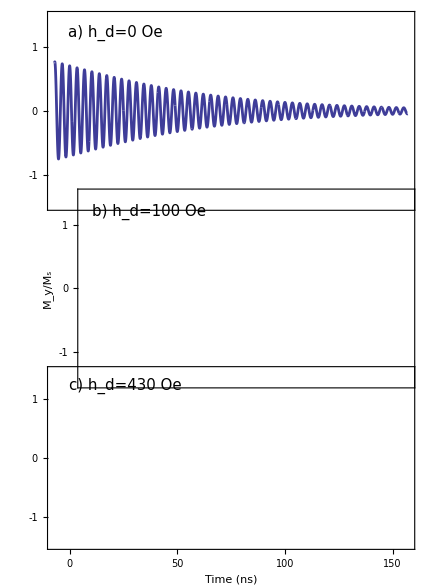

```mathematica
GraphicsColumn[{p1,p2,p3},Spacings->-56.2]
```

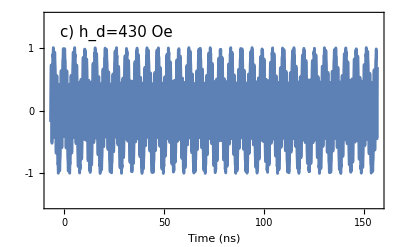

```mathematica
p3
```

```mathematica
SetDirectory["/Users/mgp333/Desktop/mathematica/"];
```

```mathematica
outlinedGraphics=First@ImportString[ExportString[p3,"EPS"],"EPS","TextMode"->"Outlines"]
```

```mathematica
Export["time.eps",p3];
```

Capital M, top grid

#### FFT Column

```mathematica
f10=ListLinePlot[Transpose[{ff[0,0,50,0.01],yff[0,0,50,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[1,.91,.07,.1]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f20=ListLinePlot[Transpose[{ff[0.1,0,50,0.01],yff[0.1,0,50,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[1,.91,.07,.1]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f30=ListLinePlot[Transpose[{ff[0.43,0,50,0.01],yff[0.43,0,50,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[1,.91,.07,.1]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f11=ListLinePlot[Transpose[{ff[0,50,100,0.01],yff[0,50,100,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[.59,0,.73,0.35],Dashing[{.02,.005}]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f21=ListLinePlot[Transpose[{ff[0.1,50,100,0.01],yff[0.1,50,100,0.01]}],PlotRange->{{0,1.2},{0,50}},
Frame->False,
Axes->None,
PlotStyle->{Thickness[0.005],CMYKColor[.59,0,.73,0.35],Dashing[{.02,.005}]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f31=ListLinePlot[Transpose[{ff[0.43,50,100,0.01],yff[0.43,50,100,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[.59,0,.73,0.35],Dashing[{.02,.005}]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f12=ListLinePlot[Transpose[{ff[0,150,200,0.01],yff[0,150,200,0.01]}],PlotRange->{{0,1.2},{0,50}},
(*AxesStyle->{Thickness[0.003],None},*)
Frame->True,
FrameStyle->Thickness[.004],
LabelStyle->{"FontFamily"->"Arial","FontSize"->18},FrameTicks->{{{0.2,,{0.02,0.02},{Thickness[0.004]}},{0.4,,{0.01,0.01},{Thickness[0.004]}},{0.6,,{0.02,0.02},{Thickness[0.004]}},{0.8,,{0.01,0.01},{Thickness[0.004]}},{1,,{0.02,0.02},{Thickness[0.004]}}},{{0,0,{0.02,0},{Thickness[0.004]}},{10,,{0.01,0},{Thickness[0.004]}},{20,20,{0.02,0},{Thickness[0.004]}},{30,,{0.01,0},{Thickness[0.004]}},{40,40,{0.02,0},{Thickness[0.004]}}},None,None},
PlotStyle->{Thickness[0.005],CMYKColor[0,1,1,0.1]},
Epilog->Inset[Style["a) h_d=0 Oe",FontFamily->"Arial",16],{.21,45}],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f22=ListLinePlot[Transpose[{ff[0.1,150,200,0.01],yff[0.1,150,200,0.01]}],PlotRange->{{0,1.2},{0,50}},
Frame->True,
FrameStyle->Thickness[0.004],
FrameLabel->{None,Style["",18,FontFamily->"Arial"],None,None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->18},FrameTicks->{{{0.2,,{0.02,0.02},{Thickness[0.004]}},{0.4,,{0.01,0.01},{Thickness[0.004]}},{0.6,,{0.02,0.02},{Thickness[0.004]}},{0.8,,{0.01,0.01},{Thickness[0.004]}},{1,,{0.02,0.02},{Thickness[0.004]}}},{{0,0,{0.02,0},{Thickness[0.004]}},{10,,{0.01,0},{Thickness[0.004]}},{20,20,{0.02,0},{Thickness[0.004]}},{30,,{0.01,0},{Thickness[0.004]}},{40,40,{0.02,0},{Thickness[0.004]}}},None,None},
PlotStyle->{Thickness[0.005],CMYKColor[0,1,1,0.1]},
Epilog->Inset[Style["b) h_d=100 Oe",FontFamily->"Arial",16],{.25,45}],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f32=ListLinePlot[Transpose[{ff[0.43,150,200,0.01],yff[0.43,150,200,0.01]}],PlotRange->{{0,1.2},{0,50}},
Frame->True,
FrameLabel->{Style["Frequency (GHz)",18],None,None,None},
FrameStyle->Thickness[.004],
LabelStyle->{"FontFamily"->"Arial","FontSize"->18},FrameTicks->{{{0.2,0.2,{0.02,0},{Thickness[0.004]}},{0.4,,{0.01,0},{Thickness[0.004]}},{0.6,0.6,{0.02,0},{Thickness[0.004]}},{0.8,,{0.01,0},{Thickness[0.004]}},{1,1,{0.02,0},{Thickness[0.004]}}},{{0,0,{0.02,0},{Thickness[0.004]}},{10,,{0.01,0},{Thickness[0.004]}},{20,20,{0.02,0},{Thickness[0.004]}},{30,,{0.01,0},{Thickness[0.004]}},{40,40,{0.02,0},{Thickness[0.004]}}},None,None},
PlotStyle->{Thickness[0.005],CMYKColor[0,1,1,0.1]},
Epilog->Inset[Style["c) h_d=430 Oe",FontFamily->"Arial",16],{.25,45}],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
ft1 =GraphicsColumn[{f10,f20,f30},Spacings->-56];
```

```mathematica
ft2 =GraphicsColumn[{f11,f21,f31},Spacings->-56];
```

```mathematica
ft3 =GraphicsColumn[{f12,f22,f32},Spacings->-56];
```

```mathematica
Show[{ft3,ft2,ft1}]
```

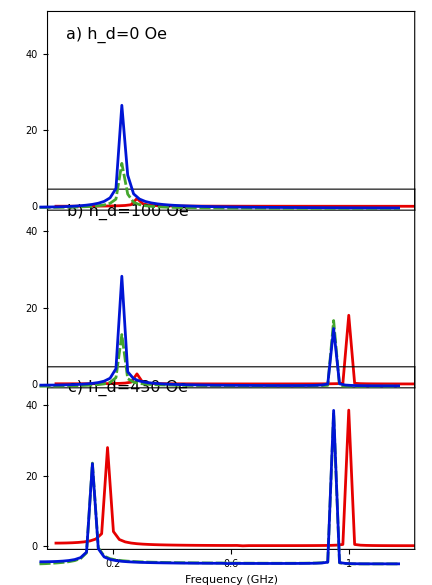

No Italics, colors? dashing?

#### Time Amp Dual

```mathematica
SetDirectory["Z:\\Magnetic Research\\mathematica\\amp_files"];
```

```mathematica
AmpPlotz1=ListPlot[{Transpose[{Amptt,AmpIm[0]}],Transpose[{Amptt,AmpIm[.37]}],Transpose[{Amptt,AmpIm[.40]}],Transpose[{Amptt,AmpIm[.43]}]},
PlotRange->{{0,10000},{0,12.5}},Frame->True,
FrameStyle->Thickness[0.004],
LabelStyle->{"FontFamily"->"Arial","FontSize"->20},
FrameTicks->{
{{2500,,{0.02,0.02},{Thickness[0.004]}},{5000,,{0.02,0.02},{Thickness[0.004]}},{7500,,{0.02,0.02},{Thickness[0.004]}},{10000,,{0,0},{Thickness[0.004]}},{1250,,{0.01,0.01},{Thickness[0.004]}},{3750,,{0.01,0.01},{Thickness[0.004]}},{6250,,{0.01,0.01},{Thickness[0.004]}},{8750,,{0.01,0.01},{Thickness[0.004]}}},
{{0,0,{0.02,0},{Thickness[0.004]}},{2.5,,{0.01,0},{Thickness[0.004]}},{5,5,{0.02,0},{Thickness[0.004]}},{7.5,,{0.01,0},{Thickness[0.004]}},{10,10,{0.02,0},{Thickness[0.004]}}},None,None},
Joined->{True,True,True,True},
PlotStyle->{{Thickness[0.01],CMYKColor[.66,.38,1,0]},{Thickness[0.01],CMYKColor[0,1,0,0.4]},{Thickness[0.01],CMYKColor[0,.62,.92,0]},{Thickness[0.01],CMYKColor[1,.91,.07,.32]}},
ImagePadding->{{61,40},{60,10}},
ImageSize->500];
```

```mathematica
AmpPlotz2=ListPlot[{Transpose[{Amptt,AmpIm[0.43]}],Transpose[{Amptt,AmpIm[.46]}],Transpose[{Amptt,AmpIm[.50]}],Transpose[{Amptt,AmpIm[.70]}]},
PlotRange->{{0,10000},{0,12.5}},Frame->True,
FrameStyle->Thickness[0.004],
FrameLabel->{"Time (ns)","",None,None},
LabelStyle->{"FontFamily"->"Arial","FontSize"->20},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.004]}},{5000,5000,{0.02,0},{Thickness[0.004]}},{7500,7500,{0.02,0},{Thickness[0.004]}},{10000,10000,{0,0},{Thickness[0.004]}},{1250,,{0.01,0},{Thickness[0.004]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.004]}},{8750,,{0.01,0},{Thickness[0.004]}}},
{{0,0,{0.02,0},{Thickness[0.004]}},{2.5,,{0.01,0},{Thickness[0.004]}},{5,5,{0.02,0},{Thickness[0.004]}},{7.5,,{0.01,0},{Thickness[0.004]}},{10,10,{0.02,0},{Thickness[0.004]}}},None,None},
Joined->{True,True,True,True},
PlotStyle->{{Thickness[0.01],CMYKColor[1,.91,.07,.32]},{Thickness[0.01],CMYKColor[0,0,1,0.18]},{Thickness[0.01],CMYKColor[0,1,1,0.2]},{Thickness[0.01],CMYKColor[1,.22,.11,0]}},
(*PlotStyle->{CMYKColor[1,.91,.07,.32],CMYKColor[0,0,1,0.18],CMYKColor[0,1,1,0.2],CMYKColor[1,.22,.11,0]},*)
ImagePadding->{{61,40},{60,10}},
ImageSize->500];
```

```mathematica
GraphicsColumn[{AmpPlotz1,AmpPlotz2},Spacings->-80]
```

FFT Amplitude of Transient Peak (a.u), join lines

#### Theta Hx

```mathematica
SetDirectory["Z:\\Magnetic Research\\mathematica"];
```

```mathematica
thetarawdata = (Import["thetadata.dat","List"])*180/Pi;
```

```mathematica
hxAxis1 = Table[i,{i,0,.42,0.01}];
```

```mathematica
hxAxis2 = Table[i,{i,.43,1,0.01}];
```

```mathematica
thetadata1 = Transpose[{hxAxis1,Part[thetarawdata,1;;43]}];
```

```mathematica
thetadata2 = Transpose[{hxAxis2,Part[thetarawdata,44;;101]}];
```

```mathematica
thetapart1=ListPlot[thetadata1,
PlotRange->{{0,.9},{0,150}},
Frame->True,
FrameStyle->{{White,Thickness[0.004]},{White,Thickness[0.004]},{White,Thickness[0.004]},{White,Thickness[0.004]}},
FrameLabel->{"h_d (kOe)","<θ> (degrees)",None,None},
LabelStyle->{"FontFamily"->"Arial","FontSize"->20,White},
FrameTicks->{
{{.2,.2,{0,0},{Thickness[0.004]}},{.4,.4,{0,0},{Thickness[0.004]}},{.6,.6,{0,0},{Thickness[0.004]}},{.8,.8,{0,0},{Thickness[0.004]}},{1,1,{0,0},{Thickness[0.004]}},{.1,,{0,0},{Thickness[0.004]}},{.3,,{0,0},{Thickness[0.004]}},{.5,,{0,0},{Thickness[0.004]}},{.7,,{0,0},{Thickness[0.004]}},{.9,,{0,0},{Thickness[0.004]}}},
{{0,0,{0,0},{Thickness[0.004]}},{30,30,{0,0},{Thickness[0.004]}},{60,60,{0,0},{Thickness[0.004]}},{90,90,{0,0},{Thickness[0.004]}},{120,120,{0,0},{Thickness[0.004]}},{10,,{0,0},{Thickness[0.004]}},{20,,{0,0},{Thickness[0.004]}},{40,,{0,0},{Thickness[0.004]}},{50,,{0,0},{Thickness[0.004]}},{70,,{0,0},{Thickness[0.004]}},{80,,{0,0},{Thickness[0.004]}},{100,,{0,0},{Thickness[0.004]}},{110,,{0,0},{Thickness[0.004]}},{130,,{0,0},{Thickness[0.004]}},{150,150,{0,0},{Thickness[0.004]}}},None,None},
Joined->True,
(*Epilog->Inset[Show[{mtplotTheta[.42,2000,2050,0.01]},ImageSize->200],{.65,25}],*)
PlotStyle->{Thickness[0.008],CMYKColor[0,1,0,0.6]},
ImageSize->500];
```

```mathematica
thetapart2=ListPlot[thetadata2,
PlotRange->{{0,.9},{0,150}},
Frame->True,
FrameStyle->Thickness[0.004],
FrameLabel->{"h_d (kOe)","<θ> (degrees)",None,None},
LabelStyle->{"FontFamily"->"Arial","FontSize"->20},
FrameTicks->{
{{.2,.2,{0.02,0},{Thickness[0.004]}},{.4,.4,{0.02,0},{Thickness[0.004]}},{.6,.6,{0.02,0},{Thickness[0.004]}},{.8,.8,{0.02,0},{Thickness[0.004]}},{1,1,{0.02,0},{Thickness[0.004]}},{.1,,{0.01,0},{Thickness[0.004]}},{.3,,{0.01,0},{Thickness[0.004]}},{.5,,{0.01,0},{Thickness[0.004]}},{.7,,{0.01,0},{Thickness[0.004]}},{.9,,{0.01,0},{Thickness[0.004]}}},
{{0,0,{0.02,0},{Thickness[0.004]}},{30,30,{0.02,0},{Thickness[0.004]}},{60,60,{0.02,0},{Thickness[0.004]}},{90,90,{0.02,0},{Thickness[0.004]}},{120,120,{0.02,0},{Thickness[0.004]}},{10,,{0.01,0},{Thickness[0.004]}},{20,,{0.01,0},{Thickness[0.004]}},{40,,{0.01,0},{Thickness[0.004]}},{50,,{0.01,0},{Thickness[0.004]}},{70,,{0.01,0},{Thickness[0.004]}},{80,,{0.01,0},{Thickness[0.004]}},{100,,{0.01,0},{Thickness[0.004]}},{110,,{0.01,0},{Thickness[0.004]}},{130,,{0.01,0},{Thickness[0.004]}},{140,,{0.01,0},{Thickness[0.004]}},{150,150,{0.02,0},{Thickness[0.004]}}},None,None},
Joined->True,
(*Epilog->Inset[Show[{mtplotTheta[.42,2000,2050,0.01]},ImageSize->200],{.65,25}],*)
Epilog->{Thickness[0.004],Dashed,Line[{{0.425,50},{0.425,130.4}}]},
PlotStyle->{Thickness[0.008],CMYKColor[0,1,0,0.6]},
ImageSize->500];
```

```mathematica
Show[thetapart2,thetapart1]
```

Do other way with and without arrows,<>. Range from 0-1 or 0-.9?

```mathematica
mtplotTheta2[.44,2000,2051,0.01]
```

```mathematica
mtplotTheta1[.42,2000,2047,0.01]
```

```mathematica
mtplotTheta2[.44,2000,2046.02,0.01]
```

```mathematica
mtplotTheta2n[.44,2000,2046.02,0.01]
```

```mathematica
mtplotTheta1n[.42,2000,2046.02,0.01]
```

```mathematica
Graphics[{CMYKColor[0,1,1,0.1],Disk[{0,0},0.1]}]
```

```mathematica
Graphics[{CMYKColor[1,.91,.07,.05],Disk[{0,0},0.1]}]
```

```mathematica
Graphics[{CMYKColor[.59,0,.73,0.35],Disk[{0,0},0.1]}]
```

```mathematica
Graphics[{CMYKColor[0,0,1,0.18],Disk[{0,0},0.1]}]
```

```mathematica
Graphics[{CMYKColor[0,1,0,0.4],Disk[{0,0},0.1]}]
```

```mathematica
Graphics[{CMYKColor[0,.62,.92,0],Disk[{0,0},0.1]}]
```

```mathematica
Graphics[{CMYKColor[1,.22,.11,0],Disk[{0,0},0.1]}]
```

```mathematica
Decay Values
```

hx = 0:
	Initial Value: 8.55570742005591
	1/e * Initial Value: 3.14747
	Decay Time: 150 ns
	Decay Time approximate: 100 ns
    
hx = 430:
	Initial Value: 8.400817078521953
	1/e * Initial Value: 3.09049
	Decay Time: 6750 ns
	Decay Time Approximate: 6750

Factor: 45

#### Matlab vs. Mathematica

```mathematica
ttmean[start_,stop_,res_]:=Table[(2*i+res)/2,{i,start,stop-res,res}]
```

```mathematica
wolf[wEn_,start_,stop_,res_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];$a = Import[StringJoin["0.42_En",ToString[wEn],"_cal.dat"],"List"];ResetDirectory[];$b = Table[Part[$a,res/0.025*i+1],{i,start/res,stop/res}])
```

```mathematica
mat[mEn_,start_,stop_,res_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];$a = Import[StringJoin["hx_42_En",ToString[mEn],".dat"],"List"];ResetDirectory[];$b = Table[Part[$a,res/0.025*i+1],{i,start/res,stop/res}])
```

```mathematica
plotwolf[wEn_,start_,stop_,res_]:=ListLinePlot[Transpose[{tt[start,stop,res],wolf[wEn,start,stop,res]}],PlotRange->All,AxesLabel->{"t","m_y"},PlotLabel->"Mathematica"]
```

```mathematica
plotmat[mEn_,start_,stop_,res_]:=ListLinePlot[Transpose[{tt[start,stop,res],mat[mEn,start,stop,res]}],PlotRange->All,AxesLabel->{"t","m_y"},PlotLabel->"Matlab"]
```

```mathematica
plotmatwolf[wEn_,mEn_,start_,stop_,res_]:=ListLinePlot[{Transpose[{tt[start,stop,res],wolf[wEn,start,stop,res]}],Transpose[{tt[start,stop,res],mat[mEn,start,stop,res]}]},PlotLegends->{"Mathematica","Matlab"},PlotRange->All,AxesLabel->{"t","m_y"}, ImageSize->500]
```

```mathematica
Diff[wEn_,mEn_,start_,stop_,res_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];$a = Import[StringJoin["wEn",ToString[wEn],"_mEn",ToString[mEn],"_diff.dat"],"List"];ResetDirectory[];$b = Table[Part[$a,res/0.025*i+1],{i,start/res,stop/res}])
```

```mathematica
Diffmat[m1En_,m2En_,start_,stop_,res_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];$a = Import[StringJoin["mEn",ToString[m1En],"_mEn",ToString[m2En],"_diff.dat"],"List"];ResetDirectory[];$b = Table[Part[$a,res/0.025*i+1],{i,start/res,stop/res}])
```

```mathematica
Diffwolf[w1En_,w2En_,start_,stop_,res_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];$a = Import[StringJoin["wEn",ToString[w1En],"_wEn",ToString[w2En],"_diff.dat"],"List"];ResetDirectory[];$b = Table[Part[$a,res/0.025*i+1],{i,start/res,stop/res}])
```

```mathematica
Diffavg[wEn_,mEn_,start_,stop_,res_]:=(*Midpoint*)(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];$a = Import[StringJoin["wEn",ToString[wEn],"_mEn",ToString[mEn],"_diff.dat"],"List"];ResetDirectory[];$b = Table[Mean[Part[$a,IntegerPart[res/0.025*i+1];;IntegerPart[res/0.025*(i+1)+1]]],{i,start/res,stop/res-1}])
```

```mathematica
Diffavgmat[En1_,En2_,start_,stop_,res_]:=(*Midpoint*)(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];$a = Import[StringJoin["mEn",ToString[En1],"_mEn",ToString[En2],"_diff.dat"],"List"];ResetDirectory[];$b = Table[Mean[Part[$a,IntegerPart[res/0.025*i+1];;IntegerPart[res/0.025*(i+1)+1]]],{i,start/res,stop/res-1}])
```

```mathematica
Diffavgwolf[En1_,En2_,start_,stop_,res_]:=(*Midpoint*)(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];$a = Import[StringJoin["wEn",ToString[En1],"_wEn",ToString[En2],"_diff.dat"],"List"];ResetDirectory[];$b = Table[Mean[Part[$a,IntegerPart[res/0.025*i+1];;IntegerPart[res/0.025*(i+1)+1]]],{i,start/res,stop/res-1}])
```

```mathematica
DiffPlot[wEn_,mEn_,start_,stop_,res_]:=ListPlot[Transpose[{tt[start,stop,res],Diff[wEn,mEn,start,stop,res]}],AxesLabel->{"t","|Error|"},PlotLabel->"Mathematica vs. Matlab",ImageSize->650]
```

```mathematica
DiffPlotmat[m1En_,m2En_,start_,stop_,res_]:=ListPlot[Transpose[{tt[start,stop,res],Diffmat[m1En,m2En,start,stop,res]}],AxesLabel->{"t","|Error|"},PlotLabel->"Matlab",ImageSize->650]
```

```mathematica
DiffPlotwolf[w1En_,w2En_,start_,stop_,res_]:=ListPlot[Transpose[{tt[start,stop,res],Diffwolf[w1En,w2En,start,stop,res]}],AxesLabel->{"t","|Error|"},PlotLabel->"Matlab",ImageSize->650]
```

```mathematica
DiffavgPlot[wEn_,mEn_,start_,stop_,res_]:=ListPlot[Transpose[{ttmean[start,stop,res],Diffavg[wEn,mEn,start,stop,res]}],AxesLabel->{"t","<|Error|>"},PlotLabel->"Mathematica vs. Matlab (midpoint avg)",ImageSize->650]
```

```mathematica
DiffavgPlotmat[m1En_,m2En_,start_,stop_,res_]:=(*Use ascending numbers*)ListPlot[Transpose[{ttmean[start,stop,res],Diffavgmat[m1En,m2En,start,stop,res]}],AxesLabel->{"t","<|Error|>"},PlotLabel->"Matlab (midpoint avg)",ImageSize->650]
```

```mathematica
DiffavgPlotwolf[w1En_,w2En_,start_,stop_,res_]:=(*Use ascending numbers*)ListPlot[Transpose[{ttmean[start,stop,res],Diffavgwolf[w1En,w2En,start,stop,res]}],AxesLabel->{"t","<|Error|>"},PlotLabel->"Mathematica (midpoint avg)",ImageSize->650]
```

```mathematica
strs =OpenAppend[ToString[testings.dat]];
```

```mathematica
WriteString[strs,ToString[454,InputForm],"\n"]
```

```mathematica
WriteString[strs,ToString[1000,InputForm],"\n"]
```

```mathematica
WriteString[strs,ToString[33334,InputForm],"\n"]
```

```mathematica
Close[strs];
```

#### 100k Mathematica vs Matlab

```mathematica
ytExStream2[0.42,0,100000,10^-4,0.025,"0.42_En4_cal.dat"];
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
ytExStream2[0.42,0,100000,10^-5,0.025,"0.42_En5_cal.dat"];
```

```mathematica
ytExStream2[0.42,0,100000,10^-6,0.025,"0.42_En6_cal.dat"];
```

```mathematica
Export["wEn4_mEn4_diff.dat",Abs[Import["0.42_En4_cal.dat","List"]-Import["hx_42_En4.dat","List"]]];
```

```mathematica
Export["wEn5_mEn4_diff.dat",Abs[Import["0.42_En5_cal.dat","List"]-Import["hx_42_En4.dat","List"]]];
```

```mathematica
Export["wEn6_mEn4_diff.dat",Abs[Import["0.42_En6_cal.dat","List"]-Import["hx_42_En4.dat","List"]]];
```

```mathematica
Export["wEn1_mEn5_diff.dat",Abs[Import["0.42_En3_cal.dat","List"]-Import["hx_42_En5.dat","List"]]];
```

```mathematica
Export["wEn2_mEn5_diff.dat",Abs[Import["0.42_En3_cal.dat","List"]-Import["hx_42_En5.dat","List"]]];
```

```mathematica
Export["wEn3_mEn5_diff.dat",Abs[Import["0.42_En3_cal.dat","List"]-Import["hx_42_En5.dat","List"]]];
```

```mathematica
Export["wEn4_mEn5_diff.dat",Abs[Import["0.42_En4_cal.dat","List"]-Import["hx_42_En5.dat","List"]]];
```

```mathematica
Export["mEn4_mEn5_diff.dat",Abs[Import["hx_42_En4.dat","List"]-Import["hx_42_En5.dat","List"]]];
```

```mathematica
Export["wEn1_wEn2_diff.dat",Abs[Import["0.42_En1_cal.dat","List"]-Import["0.42_En2_cal.dat","List"]]];
```

```mathematica
Export["wEn1_wEn3_diff.dat",Abs[Import["0.42_En1_cal.dat","List"]-Import["0.42_En3_cal.dat","List"]]];
```

```mathematica
Export["wEn1_wEn4_diff.dat",Abs[Import["0.42_En1_cal.dat","List"]-Import["0.42_En4_cal.dat","List"]]];
```

```mathematica
Export["wEn2_wEn3_diff.dat",Abs[Import["0.42_En2_cal.dat","List"]-Import["0.42_En3_cal.dat","List"]]];
```

```mathematica
Export["wEn2_wEn4_diff.dat",Abs[Import["0.42_En2_cal.dat","List"]-Import["0.42_En4_cal.dat","List"]]];
```

```mathematica
Export["wEn3_wEn4_diff.dat",Abs[Import["0.42_En3_cal.dat","List"]-Import["0.42_En4_cal.dat","List"]]];
```

#### 10k Mathematica vs Matlab

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/10k_compare_RK2"];
```

```mathematica
ytExStream2[0.42,0,10000,10^-4,0.025,"0.42_En4_cal.dat"];
```

```mathematica
Clear[$a];
```

```mathematica
Clear[str]
```

```mathematica
ytExStream2[0.42,0,10000,10^-5,0.025,"0.42_En5_cal.dat"];
```

```mathematica
Clear[$a];
```

```mathematica
Clear[str]
```

```mathematica
ytExStream2[0.42,0,10000,10^-6,0.025,"0.42_En6_cal.dat"];
```

```mathematica
Clear[$a];
```

```mathematica
Clear[str]
```

```mathematica
Export["wEn5_mEn4_diff.dat",Abs[Import["0.42_En5_cal.dat","List"]-Import["hx_42_En4.dat","List"]]];
```

```mathematica
Export["wEn6_mEn4_diff.dat",Abs[Import["0.42_En6_cal.dat","List"]-Import["hx_42_En4.dat","List"]]];
```

```mathematica
Export["wEn5_mEn5_diff.dat",Abs[Import["0.42_En5_cal.dat","List"]-Import["hx_42_En5.dat","List"]]];
```

```mathematica
Export["wEn6_mEn5_diff.dat",Abs[Import["0.42_En6_cal.dat","List"]-Import["hx_42_En5.dat","List"]]];
```

```mathematica
Export["wEn5_mEn6_diff.dat",Abs[Import["0.42_En5_cal.dat","List"]-Import["hx_42_En5.dat","List"]]];
```

```mathematica
Export["wEn6_mEn6_diff.dat",Abs[Import["0.42_En6_cal.dat","List"]-Import["hx_42_En5.dat","List"]]];
```

Same Differences

```mathematica
Export["wEn1_wEn5_diff.dat",Abs[Import["0.42_En1_cal.dat","List"]-Import["0.42_En5_cal.dat","List"]]];
```

```mathematica
Export["wEn1_wEn6_diff.dat",Abs[Import["0.42_En1_cal.dat","List"]-Import["0.42_En6_cal.dat","List"]]];
```

```mathematica
Export["wEn2_wEn5_diff.dat",Abs[Import["0.42_En2_cal.dat","List"]-Import["0.42_En5_cal.dat","List"]]];
```

```mathematica
Export["wEn2_wEn6_diff.dat",Abs[Import["0.42_En2_cal.dat","List"]-Import["0.42_En6_cal.dat","List"]]];
```

```mathematica
Export["wEn3_wEn5_diff.dat",Abs[Import["0.42_En3_cal.dat","List"]-Import["0.42_En5_cal.dat","List"]]];
```

```mathematica
Export["wEn3_wEn6_diff.dat",Abs[Import["0.42_En3_cal.dat","List"]-Import["0.42_En6_cal.dat","List"]]];
```

```mathematica
Export["wEn4_wEn5_diff.dat",Abs[Import["0.42_En4_cal.dat","List"]-Import["0.42_En5_cal.dat","List"]]];
```

```mathematica
Export["wEn4_wEn6_diff.dat",Abs[Import["0.42_En4_cal.dat","List"]-Import["0.42_En6_cal.dat","List"]]];
```

```mathematica
Export["wEn5_wEn6_diff.dat",Abs[Import["0.42_En5_cal.dat","List"]-Import["0.42_En6_cal.dat","List"]]];
```

```mathematica
TimeAmpDataTest[0.41,0.1,250]
```

```mathematica
TimeAmpDataTest[0.42,0.1,250]
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/precision"];
```

```mathematica
AbsoluteTiming[yrk4Ex[0.414703125,0,500000,1*10^-3,0.5,"0.414703125.dat"]];
```

```mathematica
yrk4Ex[0.41471875,0,500000,1*10^-3,0.5,"0.41471875.dat"];
```

```mathematica
yrk4Ex[0.414734375,0,500000,1*10^-3,0.5,"0.414734375.dat"];
```

```mathematica
yrk4Ex[0.41475,0,500000,1*10^-3,0.5,"0.41475.dat"];
```

```mathematica
TimeAmpDataP["0.414703125",1*10^-3,100,0.5];
```

```mathematica
TimeAmpDataP["0.41471875",1*10^-3,100,0.5];
```

```mathematica
TimeAmpDataP["0.414734375",1*10^-3,100,0.5];
```

```mathematica
TimeAmpDataP["0.41475",1*10^-3,100,0.5];
```

```mathematica
AmpPlotPStd["0.414703125",100]
```

```mathematica
AmpPlotPStd["0.41471875",100]
```

```mathematica
AmpPlotPStd["0.414734375",100]
```

```mathematica
AmpPlotPStd["0.41475",100]
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_10k_compare"];
```

```mathematica
data=Import["hx_42_En6.dat","Data"];
```

```mathematica
data1 =data[[All,3]];
```

```mathematica
Length[data1]
```

400001

```mathematica
Export["hx_42_En6_cal.dat",data1]
```

hx_42_En6_cal.dat

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Mid_10k"];
```

```mathematica
yrk2Ex[0.42,0,10000,10^-4,0.025,"0.42_En4_cal.dat"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/RK4_10k"];
```

```mathematica
yrk4Ex[0.42,0,10000,10^-3,0.025,"0.42_En3_cal.dat"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Mid_10k"];
```

```mathematica
a = Import["hx_42.dat","List"];
```

```mathematica
b = Table[i,{i,0,10000/.05}];
```

```mathematica
Do[b[[i+1]]=Part[a,2*i+1],{i,0,Length[b]-1}];
```

```mathematica
Export["rk4_explicit_comp.dat",Abs[Import["rk4_cal.dat","List"]-Import["0.42_En2_cal.dat","List"]]]
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/temp"];
```

```mathematica
Export["",Abs[Import["0.42_En3_cal.dat","List"]-Import["hx_42_En6.dat","List"]]];
```

```mathematica
Max[Import["rk4_imp_exp_comp.dat","List"]]
```

1.×10^-10

```mathematica
AbsoluteTiming[ytplot[0.42,0,100000,0.1,0.1]]
```

#### Accuracy Test

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Mid_10k"];
```

```mathematica
Length[Import["hx_42.dat","List"]]
```

```mathematica
Length[Import["0.42_En4_cal.dat","List"]]
```

```mathematica
Export["rk2_explicit_comp.dat",Abs[Import["0.42_En4_cal.dat","List"]-Import["hx_42.dat","List"]]];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Mid_10k"];
```

```mathematica
Length[Import["0.42_En2_cal.dat","List"]]
```

```mathematica
Export["rk4_explicit_comp.dat",Abs[Import["0.42_En2_cal.dat","List"]-["hx_42.dat","List"]]];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/temp"];
```

```mathematica
yLSODAEx[0.42,0,10000,10^-3,.025,"LSODA_En3.dat"];
```

```mathematica
Export["LSODA_comp.dat",Abs[Import["LSODA_En2.dat","List"]-["hx_42.dat","List"]]];
```

```mathematica
yrk4ImpEx[0.42,0,10000,10^-3,.025,"rk4Imp_En3.dat"];
```

```mathematica
Export["rk4Imp_comp.dat",Abs[Import["rk4Imp_En2.dat","List"]-["hx_42.dat","List"]]];
```

#### Speed Test

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Mid_10k"];
```

```mathematica
Length[Import["hx_42.dat","List"]]
```

```mathematica
Length[Import["0.42_En4_cal.dat","List"]]
```

```mathematica
Export["rk2_explicit_comp.dat",Abs[Import["0.42_En4_cal.dat","List"]-["hx_42.dat","List"]]];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Mid_10k"];
```

```mathematica
Length[Import["0.42_En2_cal.dat","List"]]
```

```mathematica
Export["rk4_explicit_comp.dat",Abs[Import["0.42_En2_cal.dat","List"]-["hx_42.dat","List"]]];
```

```mathematica
ToString[NumberForm[-3.1298052229*10^-6,{11,10},ExponentFunction->(Null&)]]
```

```mathematica
epsExportNoFonts[exportName_,ob_]:=Module[{},Export[exportName,ob,"EPS"];
Run["/usr/local/bin/gs -sDEVICE=epswrite -dNOCACHE -sOutputFile=nofont-"<>exportName<>" -q -dbatch -dNOPAUSE "<>exportName<>" -c quit"]]
```

```mathematica
epsExportNoFonts["test1.eps",p3]
```

0

```mathematica
Export["test.pdf",p3,"EmbeddedFonts"->False]
```

test.pdf